```mathematica
(*BASELINES*)
em0=0.5;
ef0 = 1-em0;
(*Now using numbers for baseline life history values from literature justifications*)
mum0=0.5;
muf0= 0.5;

sigjm0=0.6;
sigjf0=0.6;
taum0=0.1;
tauf0=0.1;

mm0=0.5;
mf0=0.5;

k0=250;
rr0=6;
wm0=0.4;
wf0=0.4;
(*_________________________________________________________________________*)
(*RESIDENTS*)

(*Male only*)
emres=em0;
efres =1-em0;
zres = z0;
cmres = 0.7;
cfres = 0.0;
ctres = cmres+cfres;

mumres=mum0*E^(-zres*ctres);
mufres=muf0*E^(-zres*ctres);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;

mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
wmres=1-((1-wm0)*E^(-cmres));
wfres= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres)));

KR=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

emmres = emres*(1-mumres)*mmres;
emfres = efres* (1-mufres)*mfres;
esmres= emres*(1-mumres);
esfres = efres* (1-mufres);
amres = emres*(1-mumres)*mmres*sigjmres;
afres = efres* (1-mufres)* mfres*sigjfres;

AR =KR*(1-((wmres*amres+wfres*afres)*(mumres*emres + mufres*efres + mmres*esmres + mfres*esfres)/((emmres*sigjmres+emfres*sigjfres)*rres*afres)));


(*Female only*)
emres=em0;
efres =1-em0;

zres2 = z0;
cmres2 = 0.0;
cfres2 = 0.7;
ctres2 = cmres2+cfres2;

mumres2=mum0*E^(-zres2*ctres2);
mufres2=muf0*E^(-zres2*ctres2);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
KR2=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

wmres2=1-((1-wm0)*E^(-cmres2));
wfres2= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres2)));

emmres2 = emres*(1-mumres2)*mmres;
emfres2 = efres* (1-mufres2)*mfres;
esmres2= emres*(1-mumres2);
esfres2 = efres* (1-mufres2);
amres2 = emres*(1-mumres2)*mmres*sigjmres;
afres2 = efres* (1-mufres2)* mfres*sigjfres;

AR2 =KR2*(1-((wmres2*amres2+wfres2*afres2)*(mumres2*emres + mufres2*efres + mmres*esmres2 + mfres*esfres2)/((emmres2*sigjmres+emfres2*sigjfres)*rres*afres2)));


(*Biparental*)
emres=em0;
efres =1-em0;

zres3 = z0;
cmres3 = 0.35;
cfres3 = 0.35;
ctres3 = cmres3+cfres3;

mumres3=mum0*E^(-zres3*ctres3);
mufres3=muf0*E^(-zres3*ctres3);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
KR3=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

wmres3=1-((1-wm0)*E^(-cmres3));
wfres3= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres3)));

emmres3 = emres*(1-mumres3)*mmres;
emfres3 = efres* (1-mufres3)*mfres;
esmres3= emres*(1-mumres3);
esfres3 = efres* (1-mufres3);
amres3 = emres*(1-mumres3)*mmres*sigjmres;
afres3 = efres* (1-mufres3)* mfres*sigjfres;

AR3 =KR3*(1-((wmres3*amres3+wfres3*afres3)*(mumres3*emres + mufres3*efres + mmres*esmres3 + mfres*esfres3)/((emmres3*sigjmres+emfres3*sigjfres)*rres*afres3)));


(*No care*)

emres=em0;
efres =1-em0;

zres4 = z0;
cmres4 = 0.0;
cfres4 = 0.0;
ctres4 = cmres4+cfres4;

mumres4=mum0*E^(-zres4*ctres4);
mufres4=muf0*E^(-zres4*ctres4);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
KR4=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

wmres4=1-((1-wm0)*E^(-cmres4));
wfres4= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres4)));

emmres4 = emres*(1-mumres4)*mmres;
emfres4= efres* (1-mufres4)*mfres;
esmres4= emres*(1-mumres4);
esfres4 = efres* (1-mufres4);
amres4 = emres*(1-mumres4)*mmres*sigjmres;
afres4 = efres* (1-mufres4)* mfres*sigjfres;

AR4 =KR4*(1-((wmres4*amres4+wfres4*afres4)*(mumres4*emres + mufres4*efres + mmres*esmres4 + mfres*esfres4)/((emmres4*sigjmres+emfres4*sigjfres)*rres*afres4)));



(*MUTANTS*)

(*Male only care*)
(*z4=1;*)
z4=z0;
cm4=0.7;
cf4=0.0;
ct4 = cm4 + cf4;

mum4=mum0*E^(-z4*ct4);
muf4=muf0*E^(-z4*ct4);

em=em0;
ef = 1-em;
sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm=1-((1-mm0)*E^(-((1-mum0)*em)));
mf=1-((1-mf0)*E^(-((1-muf0)*ef)));

k4=k0;
rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef))/2);

wm4=1-((1-wm0)*E^(-cm4));
wf4=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf4)));

emm4 = em*(1-mum4)*mm;
emf4 = ef* (1-muf4)*mf;
esm4 = em*(1-mum4);
esf4 = ef*(1-muf4);
am4 = em*(1-mum4)*mm*sigjm;
af4= ef* (1-muf4)* mf*sigjf;


(*Female only care*)
(*z2=1;*)
z2=z0;
cm2=0.0;
cf2=0.7;
ct2 = cm2 + cf2;
ct2;
em=em0;
ef = 1-em;

mum2=mum0*E^(-z2*ct2);
muf2=muf0*E^(-z2*ct2);

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm=1-((1-mm0)*E^(-((1-mum0)*em)));
mf=1-((1-mf0)*E^(-((1-muf0)*ef)));

k2=k0;
rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef))/2);

wm2=1-((1-wm0)*E^(-cm2));
wf2=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf2)));

emm2 = em*(1-mum2)*mm;
emf2 = ef* (1-muf2)*mf;
esm2 = em*(1-mum2);
esf2 = ef*(1-muf2);
am2 = em*(1-mum2)*mm*sigjm;
af2 = ef* (1-muf2)* mf*sigjf;
```

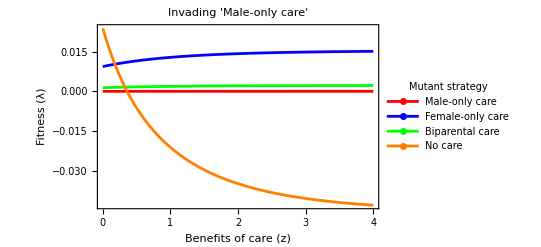

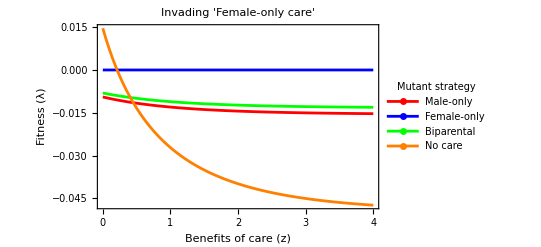

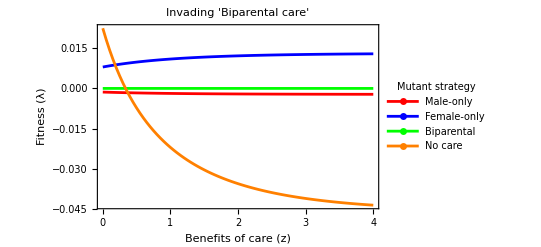

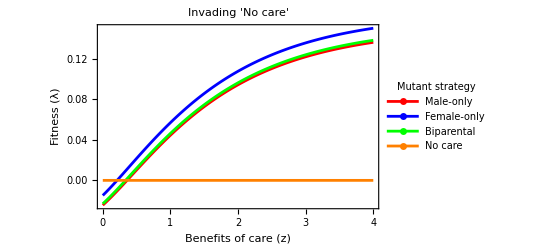

```mathematica
(*Biparental care*)
(*z3=1;*)
z3=z0;
cm3=0.35;
cf3=0.35;
ct3 = cm3 + cf3;
ct3;

mum3=mum0*E^(-z3*ct3);
muf3=muf0*E^(-z3*ct3);

wm3=1-((1-wm0)*E^(-cm3));
wf3=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf3)));

emm3 = em*(1-mum3)*mm;
emf3 = ef* (1-muf3)*mf;
esm3 = em*(1-mum3);
esf3 = ef*(1-muf3);
k3=k0;

am3 = em*(1-mum3)*mm*sigjm;
af3 = ef* (1-muf3)* mf*sigjf;


(*No care *)
(*z=1;*)
z=z0;
cm=0.0;
cf=0.0;
ct = cm + cf;

mum=mum0*E^(-z*ct);
muf=muf0*E^(-z*ct);

em=em0;
ef = 1-em0;
sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm=1-((1-mm0)*E^(-((1-mum0)*em)));
mf=1-((1-mf0)*E^(-((1-muf0)*ef)));
k=k0;
rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef))/2);

wm=1-((1-wm0)*E^(-cm));
wf=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf)));

emm = em*(1-mum)*mm;
emf = ef* (1-muf)*mf;
esm = em*(1-mum);
esf = ef*(1-muf);
am = em*(1-mum)*mm*sigjm;
af = ef* (1-muf)* mf*sigjf;




(*Invading MALE only care*)
(*Male only care mutant*)
a=-(mum4*em+muf4*ef+mm*esm4+mf*esf4);
b = rr*af4*(1-(AR/k4));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
mat={{-λ+a,b},{c,-λ+d}};
MatrixForm[mat];
res=Table[{z4,Max[λ/.Solve[Det[mat]==0,λ]]},{z0,0.0,4,0.05}];

(*Female only care mutant*)
a2=-(mum2*em+muf2*ef+mm*esm2+mf*esf2);
b2 = rr*af2*(1-(AR/k2));
c2=emm2*sigjm*(1-λ*taum)+emf2*sigjf*(1-λ*tauf);
d2 = -(wm2*am2+wf2*af2);
mat2={{-λ+a2,b2},{c2,-λ+d2}};
MatrixForm[mat2];
res20=Table[{z2,Max[λ/.Solve[Det[mat2]==0,λ]]},{z0,0.0,4,0.05}];


(*Biparental care mutant*)
a3=-(mum3*em+muf3*ef+mm*esm3+mf*esf3);
b3 = rr*af3*(1-(AR/k3));
c3=emm3*sigjm*(1-λ*taum)+emf3*sigjf*(1-λ*tauf);
d3 = -(wm3*am3+wf3*af3);
mat3={{-λ+a3,b3},{c3,-λ+d3}};
MatrixForm[mat3];
res30=Table[{z3,Max[λ/.Solve[Det[mat3]==0,λ]]},{z0,0.0,4,0.05}];


(*No care mutant*)
a4=-(mum*em+muf*ef+mm*esm+mf*esf);
b4 = rr*af*(1-(AR/k));
c4=emm*sigjm*(1-λ*taum)+emf*sigjf*(1-λ*tauf);
d4= -(wm*am+wf*af);
mat4={{-λ+a4,b4},{c4,-λ+d4}};
MatrixForm[mat4];
res40=Table[{z,Max[λ/.Solve[Det[mat4]==0,λ]]},{z0,0.0,4,0.05}];


(*Above, all initial matrices defined with AR which is male only care resident*)

(*Invading FEMALE only care*)
(*Male only mutant*)
(*a=-(mum4*em+muf4*ef+mm*esm4+mf*esf4)*)
b02 = rr*af4*(1-(AR2/k4));
(*c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4)*)
mat02={{-λ+a,b02},{c,-λ+d}};
MatrixForm[mat02];
res02=Table[{z4,Max[λ/.Solve[Det[mat02]==0,λ]]},{z0,0,4,0.05}];


(*Female only mutant*)
b22 = rr*af2*(1-(AR2/k2));
mat22={{-λ+a2,b22},{c2,-λ+d2}};
MatrixForm[mat22];
res22=Table[{z2,Max[λ/.Solve[Det[mat22]==0,λ]]},{z0,0,4,0.05}];

(*Biparental mutant *)
b32 = rr*af3*(1-(AR2/k));
mat32={{-λ+a3,b32},{c3,-λ+d3}};
MatrixForm[mat32];
res32=Table[{z3,Max[λ/.Solve[Det[mat32]==0,λ]]},{z0,0,4,0.05}];

(*No care mutant*)
b42 = rr*af*(1-(AR2/k));
mat42={{-λ+a4,b42},{c4,-λ+d4}};
MatrixForm[mat42];
res42=Table[{z,Max[λ/.Solve[Det[mat42]==0,λ]]},{z0,0,4,0.05}];


(*Invading BIPARENTAL care*)
(*Male only mutant*)
b03 = rr*af4*(1-(AR3/k4));
mat03={{-λ+a,b03},{c,-λ+d}};
MatrixForm[mat03];
res03=Table[{z4,Max[λ/.Solve[Det[mat03]==0,λ]]},{z0,0,4,0.05}];


(*Female only mutant*)
b23 = rr*af2*(1-(AR3/k2));
mat23={{-λ+a2,b23},{c2,-λ+d2}};
MatrixForm[mat23];
res23=Table[{z2,Max[λ/.Solve[Det[mat23]==0,λ]]},{z0,0,4,0.05}];

(*Biparental mutant *)
b33 = rr*af3*(1-(AR3/k3));
mat33={{-λ+a3,b33},{c3,-λ+d3}};
MatrixForm[mat33];
res33=Table[{z3,Max[λ/.Solve[Det[mat33]==0,λ]]},{z0,0,4,0.05}];

(*No care mutant*)
b43 = rr*af*(1-(AR3/k));
mat43={{-λ+a4,b43},{c4,-λ+d4}};
MatrixForm[mat43];
res43=Table[{z,Max[λ/.Solve[Det[mat43]==0,λ]]},{z0,0,4,0.05}];



(*Invading NO CARE*)
(*Male only mutant*)

a=-(mum4*em+muf4*ef+mm*esm4+mf*esf4);
b04 = rr*af4*(1-(AR4/k4));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
mat={{-λ+a,b04},{c,-λ+d}};
MatrixForm[mat];
res04=Table[{z4,Max[λ/.Solve[Det[mat]==0,λ]]},{z0,0.0,4,0.05}];


(*Female only mutant*)
b24 = rr*af2*(1-(AR4/k2));
mat24={{-λ+a2,b24},{c2,-λ+d2}};
MatrixForm[mat24];
res24=Table[{z2,Max[λ/.Solve[Det[mat24]==0,λ]]},{z0,0.0,4,0.05}];

(*Biparental mutant *)
b34 = rr*af3*(1-(AR4/k3));
mat34={{-λ+a3,b34},{c3,-λ+d3}};
MatrixForm[mat34];
res34=Table[{z3,Max[λ/.Solve[Det[mat34]==0,λ]]},{z0,0.0,4,0.05}];

(*No care mutant*)
b44 = rr*af*(1-(AR4/k));
mat44={{-λ+a4,b44},{c4,-λ+d4}};
MatrixForm[mat44];
res44=Table[{z,Max[λ/.Solve[Det[mat44]==0,λ]]},{z0,0.0,4,0.05}];



(*Invading male only care plot*)
ListPlot[
{res,res20,res30,res40},
Joined ->{True, True},
PlotLegends->LineLegend[{"Male-only care","Female-only care",  "Biparental care", "No care"},
LegendLabel-> "Mutant strategy",
LegendMarkers->"Line" ,
LegendMarkerSize->10,
LabelStyle ->{FontSize->14}, LegendMargins ->5
],
Frame->{True,True, False, False},
FrameLabel->{Style["Benefits of care (z)",16], Style[Rotate[Column[{"Fitness","(λ)"},Alignment-> Center], 270 Degree],16]},LabelStyle->Black,
PlotLabel-> Style["Invading 'Male-only care'",18],
ImageSize-> 400,
PlotStyle  -> {Red,Blue,Green, Orange},
BaseStyle -> {FontSize -> 13}
]

(*Invading female only care plot*)
ListPlot[
{res02,res22,res32,res42},
Joined ->{True, True},
PlotLegends->LineLegend[{"Male-only","Female-only", "Biparental", "No care"},
LegendLabel-> "Mutant strategy",
LegendMarkers->"Line" ,
LegendMarkerSize->10,
LabelStyle ->{FontSize->14}, LegendMargins->5
],
Frame->{True,True, False, False},
FrameLabel->{Style["Benefits of care (z)",16], Style[Rotate[Column[{"Fitness","(λ)"},Alignment-> Center], 270 Degree],16]}, LabelStyle -> Black,
PlotLabel->Style[ "Invading 'Female-only care'",18],
ImageSize-> 400,
PlotStyle  -> {Red,Blue, Green, Orange},
BaseStyle -> {FontSize -> 13}
]

(*Invading biparental care plot*)
ListPlot[
{res03,res23,res33, res43},
Joined ->{True, True},
PlotLegends->LineLegend[{"Male-only","Female-only", "Biparental", "No care"},
LegendLabel-> "Mutant strategy",
LegendMarkers->"Line" ,
LegendMarkerSize->10,
LabelStyle ->{FontSize->14},LegendMargins ->5
],
Frame->{True,True,False, False},
FrameLabel->{Style["Benefits of care (z)",16], Style[Rotate[Column[{"Fitness","(λ)"},Alignment-> Center], 270 Degree], 16]}, LabelStyle-> Black,
PlotLabel-> Style["Invading 'Biparental care'", 18],
ImageSize-> 400,
PlotStyle  -> {Red,Blue, Green, Orange},
BaseStyle -> {FontSize -> 13}
]

(*Invading no care plot*)
ListPlot[
{res04,res24,res34, res44},
Joined ->{True, True},
PlotLegends->LineLegend[{"Male-only","Female-only", "Biparental", "No care"},
LegendLabel-> Column[{"Mutant strategy"}, Alignment -> Center],
LegendMarkers->"Line" ,
LegendMarkerSize->10,
LabelStyle ->{FontSize->14}, LegendMargins ->5
], Frame -> {True, True, False, False},
FrameLabel->{Style["Benefits of care (z)", 16], Style[Rotate[Column[{"Fitness","(λ)"},Alignment-> Center], 270 Degree],16, "Black"]},
LabelStyle-> Black,
PlotLabel-> Style["Invading 'No care' ", 18, "Black"],
ImageSize-> 400,
PlotStyle  -> {Red,Blue,Green, Orange},
BaseStyle -> {FontSize -> 13}
]
```